```mathematica
a = 1; b=-1; c=1;
x = 0.01;
Q = 8;
z = 0.4;
pT = 2.0;
Λ = 0.3;
Qs0 = 1;
W2 = Q^2(1/x-1);


Qu[r_, pT_, Q_]:=( a Log[W2/Λ^2]+ b Log[1/(r^2 Λ^2)] + c) BesselJ[1, pT r] BesselK[1, Q Sqrt[z(1-z)] r];
Nd[r_, pT_, Q_] := (1 -Exp[-r^2 Qs0^2/4 Log[1/(r Λ) + E] ])BesselJ[1, pT r] BesselK[1, Q Sqrt[z(1-z)] r];
ir[ξ_, r_] := Exp[-ξ r^2];


IntQu[pT_, Q_, ξ_] := Log[Abs[NIntegrate[Qu[r, pT, Q] ir[ξ, r] r, {r,0, 1/Λ}]]];
IntN[pT_, Q_, ξ_] :=Log[Abs[ NIntegrate[Nd[r, pT, Q] ir[ξ, r] r, {r,0, 1/Λ}]]];
```

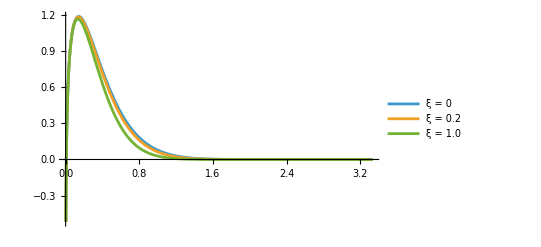

```mathematica
Plot[{Qu[r, pT, Q] ir[0, r], Qu[r,pT, Q] ir[0.2, r], Qu[r, pT, Q] ir[1.0, r]}, {r, 0, 1/Λ},
PlotLegends->{"ξ = 0", "ξ = 0.2", "ξ = 1.0"}]
```

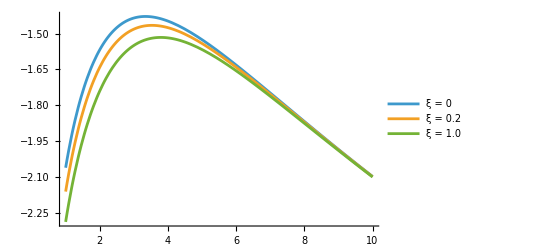

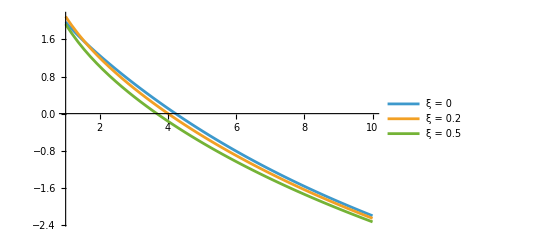

```mathematica
Plot[{IntQu[ pT, Q, 0.0] , IntQu[ pT, Q, 0.2], IntQu[ pT, Q,0.5]}, {pT, 1.0, 10},
PlotLegends->{"ξ = 0", "ξ = 0.2", "ξ = 1.0"}, PlotRange->All]

Plot[{IntQu[ pT, Q, 0.0] , IntQu[ pT, Q, 0.2], IntQu[ pT, Q,0.5]}, {Q, 1.0, 10},
PlotLegends->{"ξ = 0", "ξ = 0.2", "ξ = 0.5"}, PlotRange->All]
```

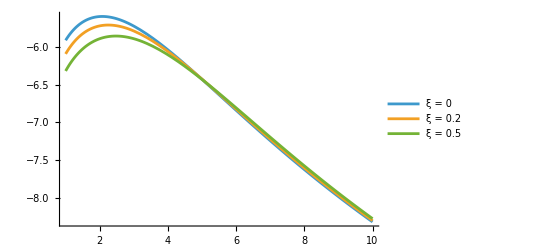

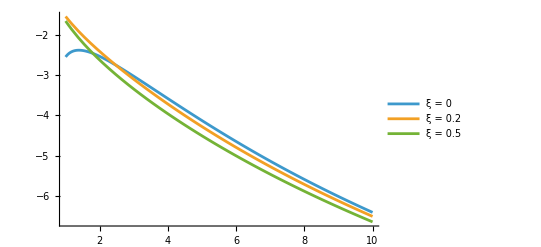

```mathematica
Plot[{IntN[ pT, Q, 0.0] , IntN[ pT, Q, 0.2], IntN[ pT, Q,0.5]}, {pT, 1, 10},
PlotLegends->{"ξ = 0", "ξ = 0.2", "ξ = 0.5"}, PlotRange->All]

Plot[{IntN[ pT, Q, 0.0] , IntN[ pT, Q, 0.2], IntN[ pT, Q,0.5]}, {Q, 1, 10},
PlotLegends->{"ξ = 0", "ξ = 0.2", "ξ = 0.5"}, PlotRange->All]
```